## Zentrierte rechteckige Bodenplatte

```mathematica
template=Polygon[{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}]
```

Polygon[{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}]

## 4503

```mathematica
Last[Solve[{w1==w+r1+r2,w2==w-r1-r2},{w,r2}]]
%/.{w1->20,w2->14,r1->3.9/2}
%%/.{w1->33.1,w2->26.9,r1->3.9/2}
```

{w→(w1+w2)/2,r2→1/2 (-2 r1+w1-w2)}

{w→17,r2→1.05}

{w→30.,r2→1.15}

```mathematica
Circle[pos,r]/.pos->#&/@{{-w/2,-l/2},{w/2,l/2},{w/2,-l},{-w/2,l}}/.{w->17,l->30,r->3.9/2}
```

{Circle[{-17/2,-15},1.95],Circle[{17/2,15},1.95],Circle[{17/2,-30},1.95],Circle[{-17/2,30},1.95]}

```mathematica
Circle[pos,r]/.pos->#&/@{{-w/2,l/2},{w/2,-l/2},{w/2,l},{-w/2,-l}}/.{w->17,l->30,r->2.2/2}
```

{Circle[{-17/2,15},1.1],Circle[{17/2,-15},1.1],Circle[{17/2,30},1.1],Circle[{-17/2,-30},1.1]}

```mathematica
dimensions4503=Flatten[{Circle[pos,r]/.pos->#&/@{{-w/2,-l/2},{w/2,l/2},{w/2,-l},{-w/2,l}}/.{w->17,l->30,r->2.2/2},Circle[pos,r]/.pos->#&/@{{-w/2,l/2},{w/2,-l/2},{w/2,l},{-w/2,-l}}/.{w->17,l->30,r->3.9/2},Circle[pos,r]/.pos->#&/@{{-w,0},{w,0}}/.{r->2.4/2,w->(9.2+4.0)/2},Circle[pos,r]/.pos->#&/@{{0,0},{0,-l},{0,l}}/.{r->3./2,l->(21+15)/2.},template/.{w->29.0,l->89.6}}]
```

{Circle[{-17/2,-15},1.1],Circle[{17/2,15},1.1],Circle[{17/2,-30},1.1],Circle[{-17/2,30},1.1],Circle[{-17/2,15},1.95],Circle[{17/2,-15},1.95],Circle[{17/2,30},1.95],Circle[{-17/2,-30},1.95],Circle[{-6.6,0},1.2],Circle[{6.6,0},1.2],Circle[{0,0},1.5],Circle[{0,-18.},1.5],Circle[{0,18.},1.5],Polygon[{{-14.5,-44.8},{-14.5,44.8},{14.5,44.8},{14.5,-44.8}}]}

## 4514

```mathematica
dimensions4514=Flatten[{Circle[pos,r]/.pos->#&/@{{-w/2,l},{w/2,l}}/.{r->3.5/2,w->(18.5+11.5)/2,l->(86.2-78.2)/2},Circle[pos,r]/.pos->#&/@{{-w/2,-l/2},{-w/2,l/2},{w/2,l/2},{w/2,-l/2}}/.{l->(142.+135.)/2,w->(22.4+15.6)/2,r->3.5/2},template/.{w->29.9,l->168.2}}]
```

{Circle[{-7.5,4.},1.75],Circle[{7.5,4.},1.75],Circle[{-9.5,-69.25},1.75],Circle[{-9.5,69.25},1.75],Circle[{9.5,69.25},1.75],Circle[{9.5,-69.25},1.75],Polygon[{{-14.95,-84.1},{-14.95,84.1},{14.95,84.1},{14.95,-84.1}}]}

## Visualisierung

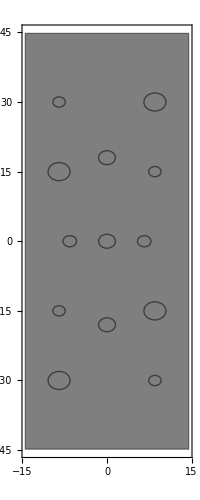

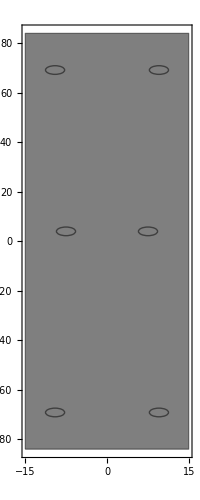

{Null,Null}

```mathematica
Print[Show[Graphics[{Thick,EdgeForm[Thick],Transparent,Opacity[0.5],#},Frame->True]]]&/@{dimensions4503,dimensions4514}
```